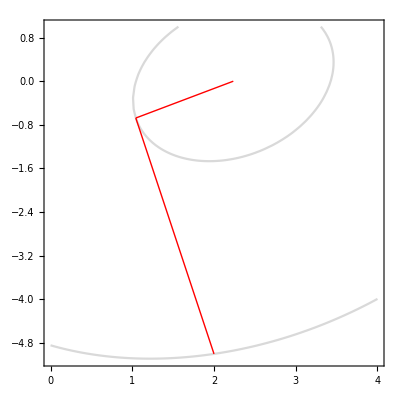

{2,53}

{2.2361,-0.000115426}

{2,82}

{2.23607,9.74881×10^-8}

```mathematica
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f1p1.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5.1,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5.1,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{2,53},{2,-5},{1.04316,-0.675334},{2.2361,-0.000116033}}

-Graphics-

{2,53}

{2.2361,-0.000116033}

{2,82}

{2.23607,9.78396×10^-8}

{{2,53},{2,-5},{1.04316,-0.675334},{2.23611,-0.000129552}}

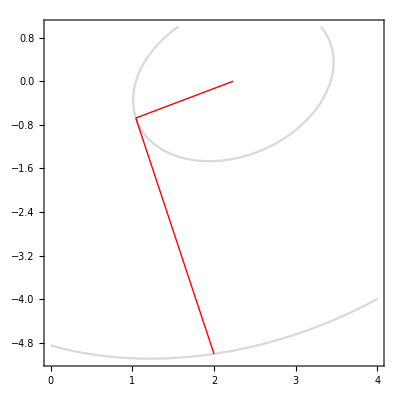

{2,53}

{2.23611,-0.000129552}

{2,82}

{2.23607,1.05658×10^-7}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-5.1,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

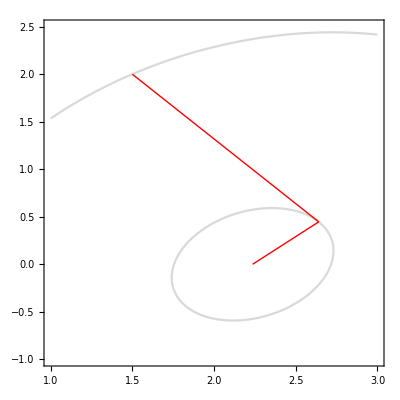

{2,57}

{2.23605,0.0000502061}

{2,85}

{2.23607,-2.45631×10^-8}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f1p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f1p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

-Graphics-

{2,57}

{2.23605,0.0000503086}

{2,85}

{2.23607,-2.45982×10^-8}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f1p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

-Graphics-

{2,57}

{2.23605,0.0000553395}

{2,85}

{2.23607,-2.63213×10^-8}

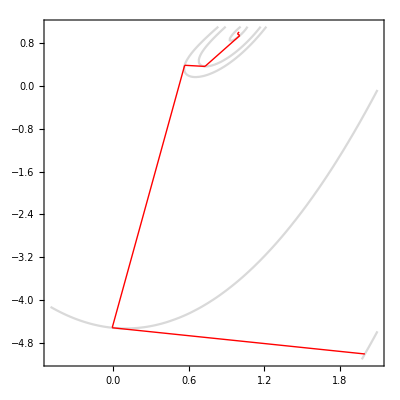

{6,202}

{0.999917,1.00014}

{7,350}

{1.,1.00001}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,1.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

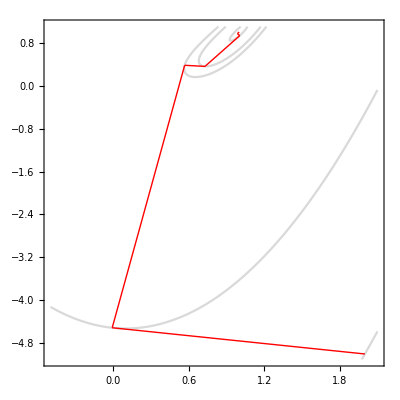

{6,198}

{0.999917,1.00014}

{7,346}

{1.,1.00001}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,1.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{8,258},{2,-5},{-0.00958234,-4.51118},{0.566786,0.380175},{0.566791,0.380175},{0.729652,0.360982},{1.00545,0.935486},{1.00545,0.935486},{0.978424,0.948458},{0.99973,1.0001}}

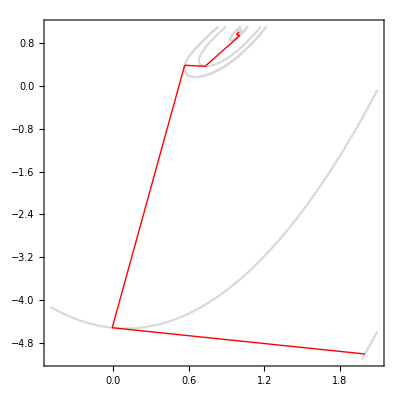

{8,258}

{0.99973,1.0001}

{10,491}

{0.999995,0.999987}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f2p1.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,1.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

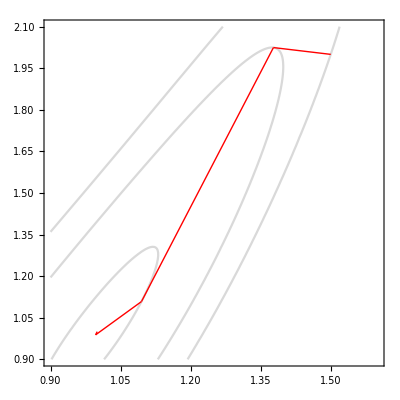

{4,139}

{0.999904,0.999879}

{5,259}

{1.,0.999999}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

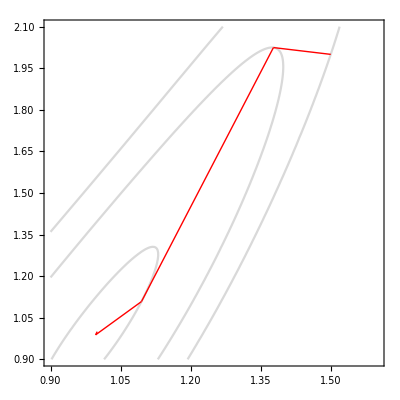

{4,138}

{0.999904,0.999879}

{5,258}

{1.,0.999999}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{7,249},{1.5,2},{1.37726,2.02455},{1.09463,1.10831},{1.09463,1.10831},{1.04958,1.12221},{1.00246,1.00065},{1.00246,1.00065},{1.00057,1.00138}}

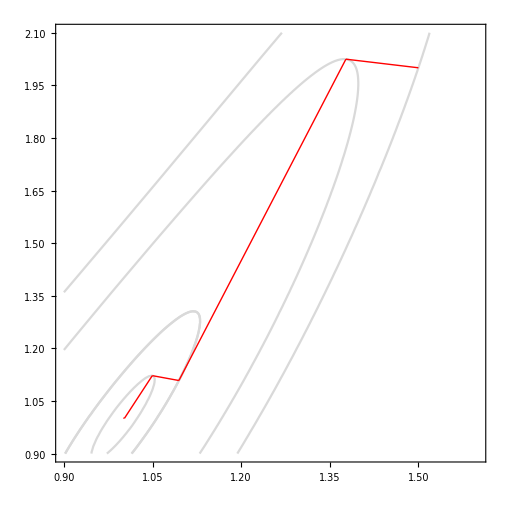

{7,249}

{1.00057,1.00138}

{8,408}

{1.,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f2p2.txt","Table"]
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

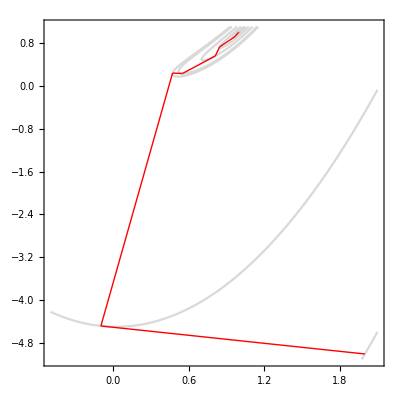

{8,240}

{0.999708,0.999249}

{9,540}

{1.,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,1.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

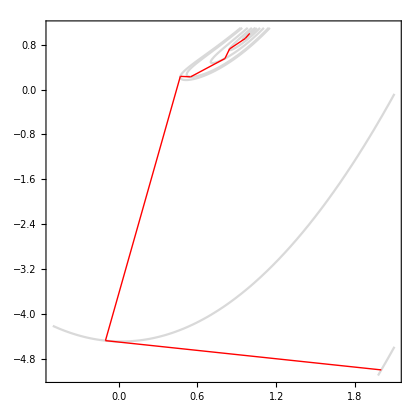

{8,226}

{0.999709,0.999251}

{9,525}

{1.,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,1.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{9,316},{2,-5},{-0.099434,-4.47804},{1.62625,2.48422},{1.56997,2.49818},{1.39042,1.84321},{1.14809,1.21628},{1.10646,1.23237},{1.02059,1.02901},{1.01498,1.03138},{1.00025,1.0001}}

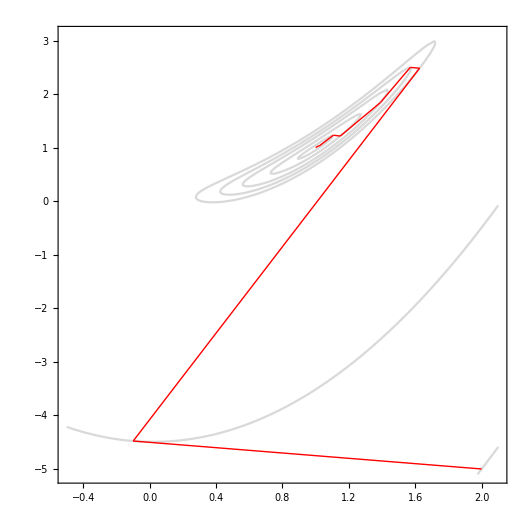

{9,316}

{1.00025,1.0001}

{10,809}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f3p1.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-0.5,2.1},{y,-5.1,3.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

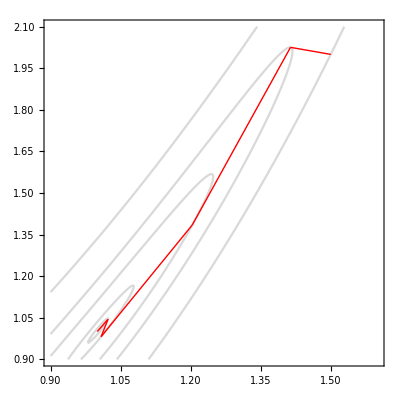

{5,167}

{1.00007,1.00031}

{7,365}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/DFPeps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

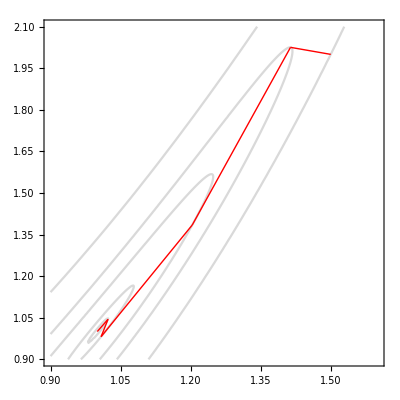

{5,165}

{1.00007,1.00031}

{7,363}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/BFSHeps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{7,335},{1.5,2},{1.4138,2.02535},{1.20339,1.38448},{1.17504,1.39379},{1.04107,1.06272},{1.03152,1.06658},{1.00106,1.00079},{1.0005,1.00105}}

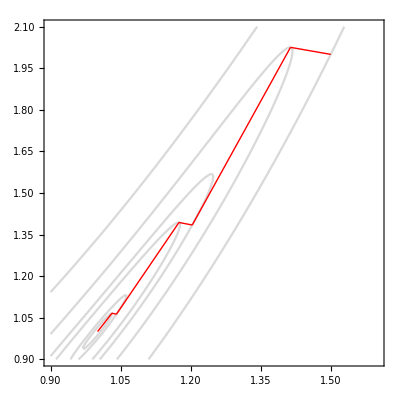

{7,335}

{1.0005,1.00105}

{9,680}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps1f3p2.txt","Table"]
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab5/lab5/PAULeps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```